Syntax::bktmcp: Expression "({#[[1]],#[[2]]},#[[3]]" has no closing ")".

```mathematica
(*Data of the initial state*)
data0=Import["/home/daniel/Documents/Codigos/RabiModel/src/output/wigner_rhot_data.dat","Table"];
```

```mathematica
(* Data of the state at time t*)
data=Import["/home/daniel/Documents/Codigos/RabiModel/src/output/wigner_rhot_data.dat","Table"];
```

```mathematica
(* =====2. Smoothing parameter=====*)
tau=0.038;

(* =====3. Extract x and p grid values=====*)
xVals=Sort[DeleteDuplicates[data[[All,1]]]];
pVals=Sort[DeleteDuplicates[data[[All,2]]]];

nx=Length[xVals];
np=Length[pVals];

(*Grid spacings*)
dx=xVals[[2]]-xVals[[1]];
dp=pVals[[2]]-pVals[[1]];

(* =====4. Build Wigner matrix=====*)
Wmat=ConstantArray[0.,{nx,np}];

Do[ix=First@FirstPosition[xVals,data[[k,1]]];
ip=First@FirstPosition[pVals,data[[k,2]]];
Wmat[[ix,ip]]=data[[k,3]],{k,Length[data]}];

(* =====5. Fourier transform=====*)
fw=Fourier[Wmat,FourierParameters->{0,1}];

(* =====6. Frequency grids=====*)
kx=2 Pi Join[Range[0,Floor[nx/2]],Range[-Ceiling[nx/2]+1,-1]]/(nx dx);
kp=2 Pi Join[Range[0,Floor[np/2]],Range[-Ceiling[np/2]+1,-1]]/(np dp);

(* =====7. Gaussian factor in Fourier space=====*)
gaussK=Table[Exp[-tau (kx[[i]]^2+kp[[j]]^2)/2],{i,nx},{j,np}];

(* =====8. Apply smoothing=====*)
fwTau=fw*gaussK;
WTau=Re[InverseFourier[fwTau,FourierParameters->{0,1}]];

(* =====9. Export back to 3-column format=====*)
smoothedData=Flatten[Table[{xVals[[i]],pVals[[j]],WTau[[i,j]]},{i,nx},{j,np}],1];

Export["wigner_smoothed.dat",smoothedData,"Table"];

(* =====10. Plot=====*)
ListDensityPlot[smoothedData,InterpolationOrder->2,PlotRange->All,FrameLabel->{"x","p"},PlotLegends->Automatic,PlotLabel->Row[{"Gaussian-smoothed Wigner function, tau = ",tau}]]
```

General::munfl: Exp[-713.236] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-727.866] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-742.645] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
ListDensityPlot[data,InterpolationOrder->2,PlotRange->All,PlotLegends->Automatic,FrameLabel->{"x","p"},PlotLabel->Row[{"Gaussian-smoothed Wigner function, tau = ",tau}]]
```

-Graphics-

```mathematica
xpint=Abs[smoothedData[[1,2]]-smoothedData[[2,2]]];
R=10;
volWt=Sum[(xpint*R^(1/2))^2*smoothedData[[i,3]],{i,1,Length[smoothedData]}]
NegWt=Sum[(xpint*R^(1/2))^2*(smoothedData[[i,3]]-Abs[smoothedData[[i,3]]]),{i,1,Length[smoothedData]}]
```

0.999308

-0.0000197808

```mathematica
(*Relative Wigner negativity of the smoothed Wigner function and Survival probability*)
xpint=Abs[smoothedData[[1,2]]-smoothedData[[2,2]]];
R=10;
Imm=0.0;
Ip=0.0;
Do[If[smoothedData[[i,3]]<0,Imm=Imm-2*π*(xpint*R^(1/2))^2*smoothedData[[i,3]]*data0[[i,3]],Ip=Ip+2*π*(xpint*R^(1/2))^2*smoothedData[[i,3]]*data0[[i,3]]],{i,1,Length[smoothedData]}]
relW=-(1/R)*Log[1-Imm/Ip];
N[relW]
ov=Ip+Imm
```

1.53641×10^-6

0.534199

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
datd=Import["Depth.dat"];
datsp=Import["SurvivalProbability_Quench1_R10.dat"];
```

```mathematica
R=10;
datdepth=Table[{datd[[i,1]],datd[[i,2]]},{i,1,Length[datd]}];
datratesmooth=Table[{datd[[i,1]],-(1/R)*Log[datd[[i,3]]]},{i,1,Length[datd]}];
datrate=Table[{datsp[[i,1]],-(1/R)*Log[datsp[[i,2]]]},{i,1,Length[datsp]}];
```

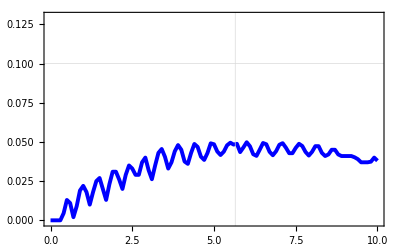

```mathematica
ListPlot[datdepth,Joined->True,PlotStyle->{{Blue,Thickness[0.007]}},PlotRange->{{0,10},{-0.001,0.13}},Frame->True,LabelStyle->{Black,16},GridLines->{{5.65},{0.1}},GridLinesStyle->{{Black},{Black,Dashed}}]
```

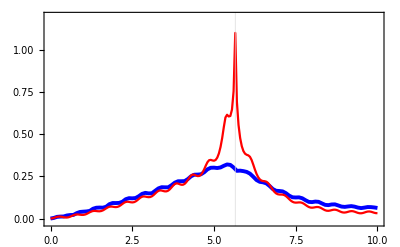

```mathematica
Show[ListPlot[{datratesmooth},Joined->True,PlotStyle->{{Blue,Thickness[0.007]},Red},PlotRange->{{0,10},{-0.02,1.2}},Frame->True,LabelStyle->{Black,16},GridLines->{{5.65},{}},GridLinesStyle->{{Black},{}},PlotLegends->Placed[{""},{0.1,0.7}]],ListPlot[datrate,Joined->True,PlotRange->All,PlotStyle->{Red},PlotLegends->Placed[{""},{0.1,0.5}]]]
```